Construcción Hamiltoniano Jaynes-Cumming

```mathematica
{ClearAll; sigmas={{0,0,1,0},{0,0,0,1},{0,0,0,0},{0,0,0,0}}; sigmen = Transpose[sigmas];a = {{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,0,1,0}}, adag = Transpose[a]; Hjc=sigmas.sigmen+adag.a+(adag.sigmen+a.sigmas)/1000};
```

Construcción condición inicial = (0,1)

```mathematica
{Ini={{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}, Inivec={0,1,0,0}};
```

```mathematica
{Ene=100, Ntemp = 0, Deltat = 5/Ene};
```

Construcción Disipadores

```mathematica
{S1=Sqrt[0.1]*Sqrt[Ntemp+1]*sigmen, S2=Sqrt[0.1]*(Ntemp)*sigmas, S3=  Sqrt[0.2]*(Ntemp+1)*a, S4= Sqrt[0.2]*(Ntemp)*adag};
```

Construcción Ecuación Maestra

```mathematica
ME[Mat_, num_]= Mat -MatrixExp[ Deltat*I*(Hjc.Mat-Mat.Hjc)+2*Deltat*(S1.Mat.Transpose[S1]+S3.Mat.Transpose[S3])-1*Deltat*(Transpose[S3].S3.Mat+Mat.Transpose[S3].S3)-1*Deltat*(Mat.Transpose[S1].S1+Transpose[S1].S1.Mat)].Mat
```

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,3.03219×10^-6+0. ⅈ,0.+2.63826×10^-8 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.-5.47362×10^-8 ⅈ,4.7625×10^-10+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.000171142+0. ⅈ}}

```mathematica
ME00= Table[Abs[Tr[Nest[ME,Ini,i].adag.a]],{i, 0,Ene}]
ME11=Table[Abs[Tr[Nest[ME,Ini,i].a.adag]],{i,0, Ene}]
MEgg =Table[Abs[Tr[Nest[ME,Ini,i].sigmas.sigmen]],{i,0, Ene}]
MEee =Table[Abs[Tr[Nest[ME,Ini,i].sigmen.sigmas]],{i,0, Ene}]
```

{0,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10,4.7625×10^-10}

{1,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811,0.00016811}

{1,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6,3.03219×10^-6}

{0,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141,0.000171141}

Construcción Quantum Jumps

```mathematica
QJ[Matvec_]=If[RandomReal[] < Abs[Deltat*Dot[S1.Matvec,S1.Matvec]], {Matvec=Normalize[S1.Matvec]},If[RandomReal[] < Abs[Deltat*Dot[S1.Matvec,S1.Matvec]]+Abs[Deltat*Dot[S3.Matvec,S3.Matvec]], Matvec=Normalize[S3.Matvec], Matvec= Normalize[MatrixExp[I*(Hjc-I/2*(Transpose[S1].S1+Transpose[S3].S3+Transpose[S2].S2+Transpose[S4].S4)*Deltat)].Matvec]] ];
```

```mathematica
QJ00= Table[Abs[Dot[a.Nest[QJ,Inivec,i],a.Nest[QJ,Inivec,i]]],{i,0,Ene}]
QJ11=Table[Abs[Dot[adag.Nest[QJ,Inivec,i],adag.Nest[QJ,Inivec,i]]], {i,0,Ene}]
QJgg =Table[Abs[Dot[sigmen.Nest[QJ,Inivec,i],sigmen.Nest[QJ,Inivec,i]]],{i,0,Ene}]
QJee =Table[Abs[Dot[sigmas.Nest[QJ,Inivec,i],sigmas.Nest[QJ,Inivec,i]]],{i,0,Ene}]
```

{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

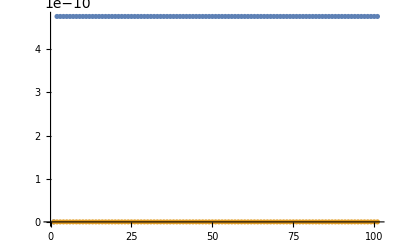

```mathematica
ListPlot[{ME00, QJ00}]
```

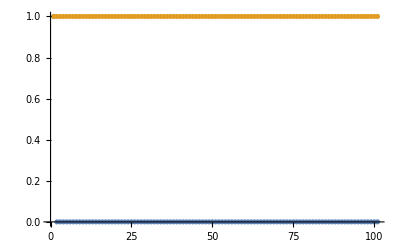

```mathematica
ListPlot[{ME11, QJ11}]
```

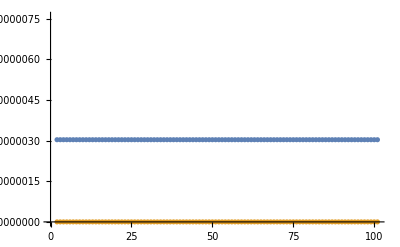

```mathematica
ListPlot[{MEgg, QJgg}]
```

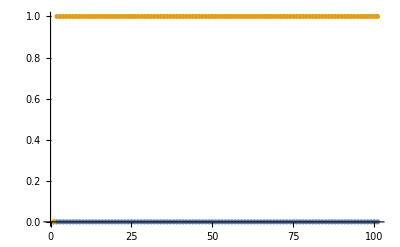

```mathematica
ListPlot[{MEee, QJee}]
```